## Numerical results for trophical transmission model with multiple infections

```mathematica
SetDirectory[NotebookDirectory[]]
<<Tools`(* Import package Tools that define useful functions*)
```

/Users/phuongnguyen/Work/multipleinfections/code

# ODEs

```mathematica
dIsdt = R[Iw, Is, Iww]- d Is- Πs[Ds, Dw, Dww] Is  - ηw  Is ;
dIwdt =  (1-p)ηw Is  - (d + αw)Iw - Πw[Ds, Dw,Dww, βw]Iw; 
dIwwdt =  p ηw Is  - (d + αww)Iww - Πww[Ds, Dw, Dww,βww]Iww; 
dDsdt =B[Ds, Dw,Dww, Is, Iw, Iww]  - μ Ds - (λww + λw) Ds;
dDwdt =(λw + 2(1-q)λww) Ds- (μ + σw) Dw - (2(1-q)λww +λw)Dw;
dDwwdt = q λww Ds + (2(1-q)λww + λw)Dw - (μ + σww)Dww;
dWdt = fw Dw +fww Dww- δ W - ηw Is;

forceInf = {ηw -> γ W, λw -> βw Iw, λww -> βww Iww};
odesRes = {dIsdt, dIwdt, dIwwdt, dDsdt, dDwdt, dDwwdt, dWdt};
varRes = {Is, Iw, Iww, Ds, Dw, Dww, W};
vartRes = {Is[t], Iw[t], Iww[t], Ds[t], Dw[t], Dww[t], W[t]};
```

# Graph format

```mathematica
includeFrame = True;
imageSize = Medium;
frameStyle = Directive[Black,Thickness[0.003]];
colorlist = ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

# Linear birth function for intermediate host

```mathematica
func0 = {R[Iw, Is, Iww] -> r(Is + Iw+Iww), Πs[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Πw[Ds, Dw,Dww, βw]->  βw(Ds + Dw+Dww),Πww[Ds, Dw,Dww, βww]->  βww(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};
sysfunc0 = odesRes/.forceInf/.func0;
sysNDSolvefunc0 = MakeSystem[varRes, t,sysfunc0];
```

## Jacobian matrix

```mathematica
Jmatfunc0 = D[sysfunc0, {varRes}];
```

## Ecological trajectories

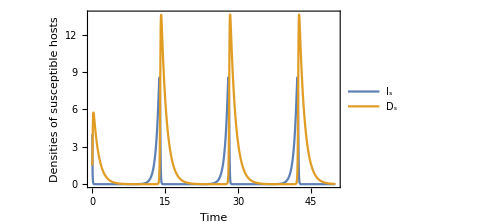
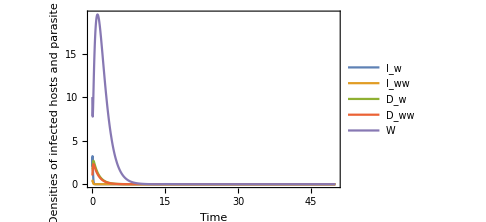
-Graphics- | -Graphics-

```mathematica
prEco0 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 0.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 6.5,fww-> 7.5, δ-> 0.9};

maxt = 50;

init0= {Is[0]== 4, Iw[0] == 2,Iww[0]==0.3, Ds[0] ==1.5, Dw[0] == 1.7,Dww[0]==1, W[0] == 10};

sols0 = NSolve[Thread[(odesRes/.func0/.forceInf/.prEco0) == 0], varRes];
ndsol0 = NDSolve[Join[sysNDSolvefunc0/.prEco0, init0], varRes, {t, 0, maxt}] ;

p1 = Plot[Evaluate[{Is[t], Ds[t]}/.ndsol0], {t, 0, maxt}, PlotRange-> {{0, maxt}, All}, PlotLegends->{"I_s",  "D_s"}, FrameLabel->{"Time", "Densities of susceptible hosts"}, ImageSize->imageSize,Frame->includeFrame,FrameStyle->frameStyle];

p2 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsol0], {t, 0, maxt}, PlotRange-> {{0, maxt}, All},PlotLegends->{"I_w", "I_ww", "D_w", "D_ww", "W"}, FrameLabel->{"Time", "Densities of infected hosts and parasite pool"}, ImageSize->imageSize, Frame-> includeFrame];
Grid[{{p1, p2}}]
(*Export["diseasefree_linear.jpg",%]*)
```

## Bifurcation γ

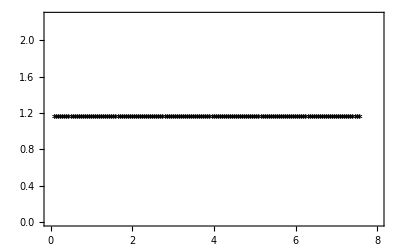

```mathematica
parγ = {ρ -> 1.2, d -> 0.1,r -> 2.5, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 1.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 1.1};
γrange = Range[0.1, 8, 0.05];

solsγ = NSolve[Thread[(odesRes/.func0/.forceInf/.parγ/.γ-> 0.1) == 0], varRes];
eqinit = {Is->1.1309523809523814,Iw->0,Iww->0,Ds->2.0000000000000004,Dw->0,Dww->0,W->0};

eqγzero = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, eqinit];
{#}& /@Transpose[{γrange, Is/.eqγzero}];
p0 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc0, parγ, γ, γrange, eqγzero], PlotStyle-> Black, Frame->includeFrame, FrameLabel->{"Pool to intermediate host transmission (γ)", "Equilibrium"}, PlotLegends->{"I_s"}];
{#}& /@Transpose[{γrange, Ds/.eqγzero}];
p1 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc0, parγ, γ, γrange, eqγzero], PlotStyle-> Gray, PlotLegends->{"D_s"}];
Show[p0, p1]
```

## Bifurcation β_w

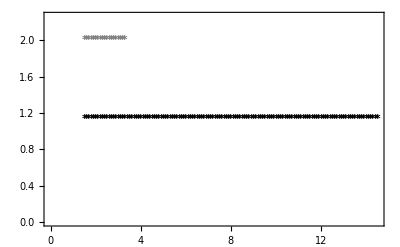

```mathematica
parβw = {ρ -> 1.2, d -> 0.1,r -> 2.5, γ -> 3.5, αw-> 0, αww-> 0,  βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 1.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 1.1, Κ-> 100};
βwrange = Range[1.5, 14.5, 0.1];

solsβw = NSolve[Thread[(sysfunc0/.parβw/.βw-> 1.5) == 0], varRes];

eqinit = {Is->1.1309523809523812,Iw->0,Iww->0,Ds->2.0000000000000004,Dw->0,Dww->0,W->0};

eqβwzero = FollowRoot[sysfunc0, parβw, βw, βwrange, varRes, eqinit];
{#}& /@Transpose[{βwrange, Is/.eqβwzero}];
p0 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc0, parβw, βw, βwrange, eqβwzero], PlotStyle-> Black, Frame->includeFrame, FrameLabel->{"Intermediate - definitive hosts transmission β_w", "Equilibrium"}, PlotLegends->{"I_s"}];
{#}& /@Transpose[{βwrange, Ds/.eqβwzero}];
p1 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc0, parβw, βw, βwrange, eqβwzero], PlotStyle-> Gray, PlotLegends->{"D_s"}];
Show[p0, p1]
```

# Nonlinear birth function for intermediate host

```mathematica
<<Tools`
```

```mathematica
func1 = {R[Iw, Is, Iww] -> r(1-k(Is + Iw+Iww))(Is + Iw+Iww), Πs[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Πw[Ds, Dw,Dww, βw]->  βw(Ds + Dw+ Dww),Πww[Ds, Dw, Dww, βww]->  βww(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};

sysfunc1 = odesRes/.forceInf/.func1;
sysNDSolvefunc1 = MakeSystem[varRes, t, sysfunc1];
```

## Jacobian matrix

```mathematica
Jmatfunc1 = D[sysfunc1, {varRes}];
```

## Ecological trajectories

## Disease free equilibrium

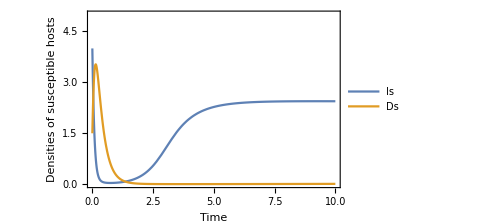
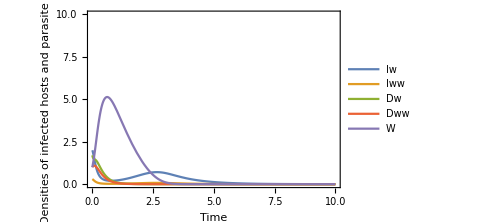
-Graphics- | -Graphics-

```mathematica
prEcoNL = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 0.9, k -> 0.26};

maxt = 10;

solsNL = NSolve[Thread[(sysfunc1/.prEcoNL) == 0], varRes];

{Is[0]== 4, Iw[0] == 2,Iww[0]==0.3, Ds[0] ==1.5, Dw[0] == 1.7,Dww[0]==1, W[0] == 1};
ndsolNL = NDSolve[Join[sysNDSolvefunc1/.prEcoNL, %], varRes, {t, 0, maxt}] ;

p1 = Plot[Evaluate[{Is[t], Ds[t]}/.ndsolNL], {t, 0, maxt}, PlotRange-> {{0, maxt}, {0, 5}}, PlotLegends->{"Is",  "Ds"},Frame->includeFrame,FrameStyle->frameStyle, FrameLabel->{"Time", "Densities of susceptible hosts"}, ImageSize->imageSize];

p2 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsolNL], {t, 0, maxt}, PlotRange->{{0, maxt},{0, 10}},PlotLegends->{"Iw", "Iww", "Dw", "Dww", "W"}, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Time", "Densities of infected hosts and parasite pool"}, ImageSize->imageSize];
Grid[{{p1, p2}}]
(*Export["Diseasefree.jpeg",%]*)
```

## Disease stable equilibrium

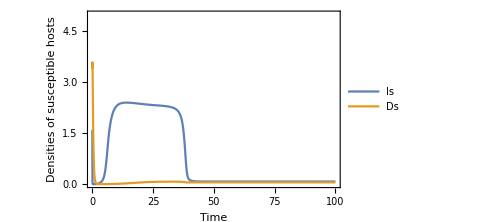
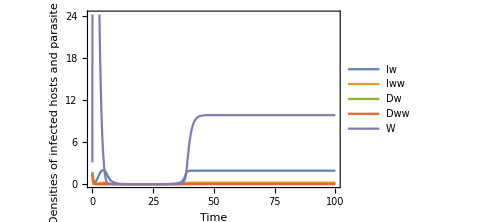
-Graphics- | -Graphics-

```mathematica
prEcoDSNL = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, α-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σ-> 0,q-> 0.01, fw -> 49, fww-> 49*8.51,δ-> 0.9, k -> 0.26};

condsimplifyNL = {αw-> α, αww-> α, σw-> σ, σww-> σ};

maxt = 100;

{Is[0]== 1.6, Iw[0] == 1.2,Iww[0]==0.32, Ds[0] ==3.4, Dw[0] == 1.7,Dww[0]==1.1, W[0] == 3.1};
ndsolDS = NDSolve[Join[sysNDSolvefunc1/.condsimplifyNL/.prEcoDSNL, %], varRes, {t, 0, maxt}, AccuracyGoal->Infinity] ;

solsDS = NSolve[Thread[(sysfunc1/.condsimplifyNL/.prEcoDSNL) == 0], varRes];

p1 = Plot[Evaluate[{Is[t], Ds[t]}/.ndsolDS], {t, 0, maxt}, PlotRange-> {{0, maxt}, {0, 5}}, PlotLegends->{"Is",  "Ds"},Frame-> includeFrame, FrameLabel->{"Time", "Densities of susceptible hosts"}, ImageSize->imageSize];
p2 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsolDS], {t, 0, maxt}, PlotRange->{{0, maxt},{0, 24.2}},PlotLegends->{"Iw", "Iww", "Dw", "Dww", "W"}, Frame-> includeFrame, FrameLabel->{"Time", "Densities of infected hosts and parasite pool"}, ImageSize->imageSize];
Grid[{{p1, p2}}]
```

## Bifurcation f_w (f_ww = ϵ f_w)

Calculation

```mathematica
parfw = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 1};
fwrangeFWrd = Range[40.5, 51.5, 0.05];
fwrangeBWrd = Range[40.5, 32, -0.05];
fwrange = Range[32, 51.5, 0.3];

(*Find all solutions of the system with the given parameter values*)
solsfwAll = NSolve[Thread[(odesRes/.func1/.forceInf/.fww-> ϵ fw/.parfw/.fw-> 40.5) == 0], varRes, Reals];

(*Select disease circulation solutions*)
solsfw= Select[solsfwAll, (Is/.#)> 0 &&(Iw/.#)> 0 &&(Iww/.#)> 0 &&(W/.#)> 0 &][[1]];

(*Select disease free solutions*)
solsfwzero = Select[solsfwAll, (Is/.#)> 0 &&(Iw/.#)== 0 &&(Iww/.#)== 0&&(Ds/.#)>0 &&(Dw/.#)== 0 &&(Dww/.#)== 0 &&(W/.#)== 0 &][[1]];

eqfwFWrd = FollowRoot[sysfunc1/.fww-> ϵ fw, parfw, fw, fwrangeFWrd, varRes, solsfw];
eqfwBWrd = FollowRoot[sysfunc1/.fww-> ϵ fw, parfw, fw, fwrangeBWrd, varRes, solsfw];

rangeIs = {{fwrangeBWrd[[-1]], fwrangeFWrd[[-1]]}, {-0.1, 2}};
rangeDs = {{fwrangeBWrd[[-1]], fwrangeFWrd[[-1]]}, {-0.01, 0.03}};
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::reged: The point {2.32041,0.000842335,0.0000935928,0.0759001,0.0000300178,0.,0.000140786} is at the edge of the search region {0.,∞} in coordinate 6 and the computed search direction points outside the region.

Plotting

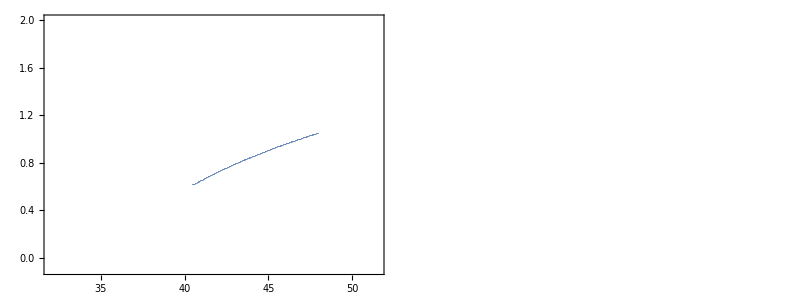

```mathematica
xaxis =fwrangeFWrd[[1;; Length[eqfwFWrd]]];
 {#}& /@Transpose[{xaxis, Iw/.eqfwFWrd}];
p0 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, xaxis, eqfwFWrd], PlotStyle->colorlist[[1]], PlotRange->rangeIs, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Parasite reproduction in single infection(f_w)", "Equilibrium I_w"}];

{#}& /@Transpose[{xaxis, Dw/.eqfwFWrd}];
p1 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, xaxis, eqfwFWrd], PlotStyle-> colorlist[[2]], PlotRange->rangeDs, ImageSize->imageSize, Frame->includeFrame, FrameLabel->{"Parasite reproduction in single infection(f_w)", "Equilibrium D_w"}];

xaxis = fwrangeBWrd[[1;;Length[eqfwBWrd]]];
{#}& /@Transpose[{xaxis, Iw/.eqfwBWrd}];
p2 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, xaxis, eqfwBWrd], PlotStyle->colorlist[[1]], PlotRange->rangeIs, ImageSize->imageSize];

{#}& /@Transpose[{xaxis, Dw/.eqfwBWrd}];
p3 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, xaxis, eqfwBWrd], PlotStyle->colorlist[[2]], PlotRange->rangeDs, ImageSize->imageSize];


eqfwzero = ConstantArray[solsfwzero, Length[fwrange]];
{#}& /@Transpose[{fwrange, Iw/.eqfwzero}];
p4 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwrange, eqfwzero], PlotStyle->colorlist[[1]], PlotRange->rangeIs, ImageSize->imageSize];

{#}& /@Transpose[{fwrange, Dw/.eqfwzero}];
p5 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwrange, eqfwzero], PlotStyle->colorlist[[2]], PlotRange->rangeDs, ImageSize->imageSize];

pp0 = Show[p0,  p2, p4];
pp1 = Show[p1, p3, p5];

Grid[{{pp0, pp1}}]
(*Export["bifurcation_fw_NL.jpg", %]*)
```

```mathematica
On[Assert];
rr= Range[35, 37, 0.02];
FollowRoot[sysfunc1/.fww-> ϵ fw, parfw, fw, rr, varRes, solsfwzero];
xx =ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, rr, %];
pos = Position[xx, "*", 1, 1][[1]][[1]];
xx[[pos]] == "*"//Assert
xx[[pos-1]] == "." //Assert
fwbifur = rr[[pos]]
```

35.84

## Bifurcation ϵ and f_w (f_ww = ϵ f_w)

```mathematica
parϵfw = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26};

ϵstart = 1.01;
ϵend = 6;
ϵinterval = 0.5;
fwstart = 35;
fwend = 45;
fwinterval = 1;
```

```mathematica
NSolveCodim2Positive[system_, commonpars_, bifurpar1_, bifurpar2_,bfparsName_, equisymbol_,variables_]:=
Module[
{sys, cpar,bfpar1, bfpar2,  vars, bfpName,eqsym,parspairVal, eqAll, eqpos},
sys = system;
cpar = commonpars;
bfpar1 = bifurpar1;
bfpar2 = bifurpar2;
bfpName = bfparsName;
eqsym = equisymbol;
vars = variables;
eqAll = NSolve[Thread[(sys/.cpar/.bfpar1/. bfpar2)==0], vars, Reals];
eqpos = Select[eqAll,And@@Thread[(vars/.# )> 0]&];
parspairVal = {bfpar1[[1]][[2]], bfpar2[[1]][[2]]};
If[eqpos != {}, Join[{bfpName -> parspairVal}, {eqsym -> eqpos[[1]]}] , Unevaluated@Sequence[]]
]
```

```mathematica
ϵfwAllresults = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parϵfw, {ϵ -> i}, {fw-> j}, ϵfw, eq,varRes],{i, ϵstart, ϵend, ϵinterval}, {j, fwstart, fwend, fwinterval}]
```

{{{ϵfw→{1.01,36},eq→{Is→2.20552,Iw→0.0961834,Iww→0.010687,Ds→0.076414,Dw→0.0032998,Dww→0.000152068,W→0.0170398}},{ϵfw→{1.01,37},eq→{Is→1.97556,Iw→0.288806,Iww→0.0320896,Ds→0.0760837,Dw→0.00908011,Dww→0.0012399,W→0.0576697}},{ϵfw→{1.01,38},eq→{Is→1.83007,Iw→0.411728,Iww→0.0457476,Ds→0.0752152,Dw→0.0121784,Dww→0.00236605,W→0.0891851}},{ϵfw→{1.01,39},eq→{Is→1.71173,Iw→0.512227,Iww→0.0569141,Ds→0.0742501,Dw→0.014388,Dww→0.00347445,W→0.119029}},{ϵfw→{1.01,40},eq→{Is→1.60916,Iw→0.599682,Iww→0.0666313,Ds→0.0732731,Dw→0.0160905,Dww→0.00454648,W→0.148619}},{ϵfw→{1.01,41},eq→{Is→1.51762,Iw→0.67797,Iww→0.07533,Ds→0.0723164,Dw→0.0174533,Dww→0.00557327,W→0.178524}},{ϵfw→{1.01,42},eq→{Is→1.43461,Iw→0.749151,Iww→0.083239,Ds→0.0713949,Dw→0.0185695,Dww→0.00655048,W→0.209034}},{ϵfw→{1.01,43},eq→{Is→1.35859,Iw→0.814481,Iww→0.0904979,Ds→0.0705156,Dw→0.0194979,Dww→0.00747625,W→0.240315}},{ϵfw→{1.01,44},eq→{Is→1.28853,Iw→0.874805,Iww→0.0972006,Ds→0.0696817,Dw→0.0202791,Dww→0.00835031,W→0.27247}},{ϵfw→{1.01,45},eq→{Is→1.22368,Iw→0.930732,Iww→0.103415,Ds→0.068894,Dw→0.020942,Dww→0.00917336,W→0.305557}}},{{ϵfw→{1.51,35},eq→{Is→2.12485,Iw→0.163502,Iww→0.0181669,Ds→0.0764766,Dw→0.00544923,Dww→0.000423409,W→0.0301754}},{ϵfw→{1.51,36},eq→{Is→1.61644,Iw→0.59347,Iww→0.0659411,Ds→0.0733459,Dw→0.015976,Dww→0.00446752,W→0.146393}},{ϵfw→{1.51,37},eq→{Is→1.45711,Iw→0.729844,Iww→0.0810938,Ds→0.071649,Dw→0.0182778,Dww→0.00628185,W→0.200414}},{ϵfw→{1.51,38},eq→{Is→1.33332,Iw→0.836229,Iww→0.0929143,Ds→0.0702171,Dw→0.0197877,Dww→0.00778948,W→0.251519}},{ϵfw→{1.51,39},eq→{Is→1.23011,Iw→0.925177,Iww→0.102797,Ds→0.0689728,Dw→0.0208787,Dww→0.00909115,W→0.302115}},{ϵfw→{1.51,40},eq→{Is→1.14128,Iw→1.00191,Iww→0.111323,Ds→0.0678768,Dw→0.021706,Dww→0.0102336,W→0.353076}},{ϵfw→{1.51,41},eq→{Is→1.06345,Iw→1.06926,Iww→0.118807,Ds→0.0669039,Dw→0.0223527,Dww→0.0112456,W→0.404789}},{ϵfw→{1.51,42},eq→{Is→0.994464,Iw→1.12905,Iww→0.12545,Ds→0.0660355,Dw→0.022869,Dww→0.0121475,W→0.457431}},{ϵfw→{1.51,43},eq→{Is→0.932837,Iw→1.18253,Iww→0.131392,Ds→0.0652571,Dw→0.0232879,Dww→0.0129549,W→0.511075}},{ϵfw→{1.51,44},eq→{Is→0.877456,Iw→1.23064,Iww→0.136738,Ds→0.0645569,Dw→0.0236321,Dww→0.0136804,W→0.565735}},{ϵfw→{1.51,45},eq→{Is→0.827452,Iw→1.27412,Iww→0.141569,Ds→0.063925,Dw→0.0239182,Dww→0.0143345,W→0.621391}}},{{ϵfw→{2.01,35},eq→{Is→2.25649,Iw→0.0538087,Iww→0.00597875,Ds→0.0762533,Dw→0.00187788,Dww→0.0000491676,W→0.00929428}},{ϵfw→{2.01,36},eq→{Is→1.05069,Iw→1.08031,Iww→0.120035,Ds→0.0667437,Dw→0.0224521,Dww→0.0114121,W→0.413999}},{ϵfw→{2.01,37},eq→{Is→0.960969,Iw→1.15811,Iww→0.128679,Ds→0.0656126,Dw→0.0231014,Dww→0.0125863,W→0.48573}},{ϵfw→{2.01,38},eq→{Is→0.885326,Iw→1.2238,Iww→0.135978,Ds→0.0646564,Dw→0.023585,Dww→0.0135774,W→0.557549}},{ϵfw→{2.01,39},eq→{Is→0.820354,Iw→1.28029,Iww→0.142255,Ds→0.0638353,Dw→0.023957,Dww→0.0144272,W→0.629843}},{ϵfw→{2.01,40},eq→{Is→0.76382,Iw→1.3295,Iww→0.147723,Ds→0.0631224,Dw→0.0242502,Dww→0.0151642,W→0.702778}},{ϵfw→{2.01,41},eq→{Is→0.714145,Iw→1.37278,Iww→0.152531,Ds→0.0624979,Dw→0.0244856,Dww→0.0158091,W→0.776411}},{ϵfw→{2.01,42},eq→{Is→0.670154,Iw→1.41113,Iww→0.156792,Ds→0.0619467,Dw→0.0246776,Dww→0.0163775,W→0.850745}},{ϵfw→{2.01,43},eq→{Is→0.63094,Iw→1.44534,Iww→0.160593,Ds→0.0614572,Dw→0.0248363,Dww→0.0168819,W→0.925756}},{ϵfw→{2.01,44},eq→{Is→0.595784,Iw→1.47603,Iww→0.164003,Ds→0.0610201,Dw→0.0249689,Dww→0.0173319,W→1.0014}},{ϵfw→{2.01,45},eq→{Is→0.564108,Iw→1.50369,Iww→0.167076,Ds→0.0606276,Dw→0.0250809,Dww→0.0177355,W→1.07765}}},{{ϵfw→{2.51,35},eq→{Is→2.28101,Iw→0.0334671,Iww→0.00371857,Ds→0.0761388,Dw→0.00117718,Dww→0.0000195752,W→0.00571145}},{ϵfw→{2.51,36},eq→{Is→0.71127,Iw→1.37528,Iww→0.152809,Ds→0.0624618,Dw→0.0244986,Dww→0.0158463,W→0.780988}},{ϵfw→{2.51,37},eq→{Is→0.658884,Iw→1.42096,Iww→0.157884,Ds→0.0618059,Dw→0.0247244,Dww→0.0165227,W→0.871389}},{ϵfw→{2.51,38},eq→{Is→0.613527,Iw→1.46054,Iww→0.162282,Ds→0.0612405,Dw→0.0249031,Dww→0.017105,W→0.962141}},{ϵfw→{2.51,39},eq→{Is→0.57385,Iw→1.49518,Iww→0.166131,Ds→0.0607482,Dw→0.0250472,Dww→0.0176115,W→1.0533}},{ϵfw→{2.51,40},eq→{Is→0.538846,Iw→1.52576,Iww→0.169529,Ds→0.0603157,Dw→0.0251653,Dww→0.018056,W→1.14488}},{ϵfw→{2.51,41},eq→{Is→0.507739,Iw→1.55294,Iww→0.172549,Ds→0.059933,Dw→0.0252634,Dww→0.0184489,W→1.23686}},{ϵfw→{2.51,42},eq→{Is→0.479918,Iw→1.57727,Iww→0.175252,Ds→0.059592,Dw→0.0253458,Dww→0.0187986,W→1.32923}},{ϵfw→{2.51,43},eq→{Is→0.454896,Iw→1.59915,Iww→0.177684,Ds→0.0592865,Dw→0.0254157,Dww→0.0191118,W→1.42196}},{ϵfw→{2.51,44},eq→{Is→0.432278,Iw→1.61894,Iww→0.179883,Ds→0.0590113,Dw→0.0254756,Dww→0.0193936,W→1.51502}},{ϵfw→{2.51,45},eq→{Is→0.411739,Iw→1.63692,Iww→0.18188,Ds→0.0587621,Dw→0.0255274,Dww→0.0196485,W→1.60838}}},{{ϵfw→{3.01,35},eq→{Is→2.29226,Iw→0.0241401,Iww→0.00268223,Ds→0.0760777,Dw→0.000852101,Dww→0.0000104368,W→0.00409709}},{ϵfw→{3.01,36},eq→{Is→0.518846,Iw→1.54324,Iww→0.171471,Ds→0.0600694,Dw→0.0252291,Dww→0.0183088,W→1.20275}},{ϵfw→{3.01,37},eq→{Is→0.485522,Iw→1.57237,Iww→0.174708,Ds→0.0596606,Dw→0.0253296,Dww→0.0187283,W→1.30977}},{ϵfw→{3.01,38},eq→{Is→0.456161,Iw→1.59805,Iww→0.177561,Ds→0.0593019,Dw→0.0254123,Dww→0.019096,W→1.41703}},{ϵfw→{3.01,39},eq→{Is→0.430094,Iw→1.62085,Iww→0.180095,Ds→0.0589847,Dw→0.0254812,Dww→0.0194207,W→1.52452}},{ϵfw→{3.01,40},eq→{Is→0.406798,Iw→1.64124,Iww→0.18236,Ds→0.0587023,Dw→0.0255394,Dww→0.0197097,W→1.63225}},{ϵfw→{3.01,41},eq→{Is→0.385856,Iw→1.65958,Iww→0.184397,Ds→0.0584493,Dw→0.0255891,Dww→0.0199683,W→1.7402}},{ϵfw→{3.01,42},eq→{Is→0.36693,Iw→1.67615,Iww→0.186239,Ds→0.0582214,Dw→0.0256318,Dww→0.0202011,W→1.84836}},{ϵfw→{3.01,43},eq→{Is→0.349745,Iw→1.6912,Iww→0.187911,Ds→0.058015,Dw→0.0256688,Dww→0.0204117,W→1.95671}},{ϵfw→{3.01,44},eq→{Is→0.334073,Iw→1.70493,Iww→0.189437,Ds→0.0578273,Dw→0.0257011,Dww→0.0206032,W→2.06523}},{ϵfw→{3.01,45},eq→{Is→0.319725,Iw→1.7175,Iww→0.190833,Ds→0.057656,Dw→0.0257296,Dww→0.0207779,W→2.17392}}},{{ϵfw→{3.51,35},eq→{Is→2.29879,Iw→0.018734,Iww→0.00208156,Ds→0.0760397,Dw→0.000662607,Dww→6.43347×10^-6,W→0.00316945}},{ϵfw→{3.51,36},eq→{Is→0.402798,Iw→1.64474,Iww→0.182749,Ds→0.0586539,Dw→0.0255491,Dww→0.0197591,W→1.652}},{ϵfw→{3.51,37},eq→{Is→0.37969,Iw→1.66498,Iww→0.184997,Ds→0.058375,Dw→0.0256032,Dww→0.0200442,W→1.77425}},{ϵfw→{3.51,38},eq→{Is→0.359067,Iw→1.68304,Iww→0.187004,Ds→0.0581269,Dw→0.0256489,Dww→0.0202976,W→1.89664}},{ϵfw→{3.51,39},eq→{Is→0.34055,Iw→1.69926,Iww→0.188806,Ds→0.0579048,Dw→0.0256879,Dww→0.0205241,W→2.01917}},{ϵfw→{3.51,40},eq→{Is→0.323832,Iw→1.7139,Iww→0.190434,Ds→0.057705,Dw→0.0257216,Dww→0.020728,W→2.14183}},{ϵfw→{3.51,41},eq→{Is→0.308664,Iw→1.72719,Iww→0.19191,Ds→0.0575241,Dw→0.0257508,Dww→0.0209123,W→2.26461}},{ϵfw→{3.51,42},eq→{Is→0.294841,Iw→1.73931,Iww→0.193257,Ds→0.0573597,Dw→0.0257764,Dww→0.0210797,W→2.38751}},{ϵfw→{3.51,43},eq→{Is→0.282193,Iw→1.7504,Iww→0.194489,Ds→0.0572096,Dw→0.0257989,Dww→0.0212325,W→2.51052}},{ϵfw→{3.51,44},eq→{Is→0.270575,Iw→1.76058,Iww→0.19562,Ds→0.057072,Dw→0.0258189,Dww→0.0213724,W→2.63362}},{ϵfw→{3.51,45},eq→{Is→0.259869,Iw→1.76997,Iww→0.196663,Ds→0.0569455,Dw→0.0258367,Dww→0.0215011,W→2.75682}}},{{ϵfw→{4.01,35},eq→{Is→0.346406,Iw→1.69413,Iww→0.188236,Ds→0.057975,Dw→0.0256758,Dww→0.0204526,W→1.97901}},{ϵfw→{4.01,36},eq→{Is→0.327255,Iw→1.7109,Iww→0.1901,Ds→0.0577458,Dw→0.0257148,Dww→0.0206863,W→2.11569}},{ϵfw→{4.01,37},eq→{Is→0.310102,Iw→1.72593,Iww→0.191771,Ds→0.0575412,Dw→0.0257481,Dww→0.0208948,W→2.25246}},{ϵfw→{4.01,38},eq→{Is→0.294648,Iw→1.73948,Iww→0.193275,Ds→0.0573574,Dw→0.0257767,Dww→0.021082,W→2.38931}},{ϵfw→{4.01,39},eq→{Is→0.280654,Iw→1.75175,Iww→0.194638,Ds→0.0571914,Dw→0.0258016,Dww→0.021251,W→2.52624}},{ϵfw→{4.01,40},eq→{Is→0.267922,Iw→1.76291,Iww→0.195879,Ds→0.0570407,Dw→0.0258233,Dww→0.0214043,W→2.66324}},{ϵfw→{4.01,41},eq→{Is→0.256289,Iw→1.77311,Iww→0.197012,Ds→0.0569033,Dw→0.0258425,Dww→0.021544,W→2.80032}},{ϵfw→{4.01,42},eq→{Is→0.245619,Iw→1.78247,Iww→0.198052,Ds→0.0567775,Dw→0.0258595,Dww→0.0216718,W→2.93747}},{ϵfw→{4.01,43},eq→{Is→0.235798,Iw→1.79108,Iww→0.199009,Ds→0.056662,Dw→0.0258746,Dww→0.0217892,W→3.07468}},{ϵfw→{4.01,44},eq→{Is→0.226728,Iw→1.79904,Iww→0.199893,Ds→0.0565554,Dw→0.0258882,Dww→0.0218973,W→3.21195}},{ϵfw→{4.01,45},eq→{Is→0.218327,Iw→1.80641,Iww→0.200712,Ds→0.0564569,Dw→0.0259004,Dww→0.0219973,W→3.34927}}},{{ϵfw→{4.51,35},eq→{Is→0.289647,Iw→1.74386,Iww→0.193763,Ds→0.057298,Dw→0.0257857,Dww→0.0211425,W→2.43672}},{ϵfw→{4.51,36},eq→{Is→0.274806,Iw→1.75687,Iww→0.195208,Ds→0.0571221,Dw→0.0258117,Dww→0.0213215,W→2.58759}},{ϵfw→{4.51,37},eq→{Is→0.261407,Iw→1.76862,Iww→0.196513,Ds→0.0569637,Dw→0.0258341,Dww→0.0214826,W→2.7385}},{ϵfw→{4.51,38},eq→{Is→0.249251,Iw→1.77928,Iww→0.197698,Ds→0.0568203,Dw→0.0258538,Dww→0.0216283,W→2.88947}},{ϵfw→{4.51,39},eq→{Is→0.238172,Iw→1.789,Iww→0.198778,Ds→0.0566899,Dw→0.025871,Dww→0.0217608,W→3.04048}},{ϵfw→{4.51,40},eq→{Is→0.228032,Iw→1.79789,Iww→0.199766,Ds→0.0565707,Dw→0.0258862,Dww→0.0218818,W→3.19154}},{ϵfw→{4.51,41},eq→{Is→0.218718,Iw→1.80606,Iww→0.200674,Ds→0.0564615,Dw→0.0258998,Dww→0.0219926,W→3.34264}},{ϵfw→{4.51,42},eq→{Is→0.210133,Iw→1.8136,Iww→0.201511,Ds→0.056361,Dw→0.025912,Dww→0.0220946,W→3.49378}},{ϵfw→{4.51,43},eq→{Is→0.202195,Iw→1.82056,Iww→0.202285,Ds→0.0562682,Dw→0.0259229,Dww→0.0221887,W→3.64496}},{ϵfw→{4.51,44},eq→{Is→0.194832,Iw→1.82702,Iww→0.203002,Ds→0.0561822,Dw→0.0259327,Dww→0.0222759,W→3.79618}},{ϵfw→{4.51,45},eq→{Is→0.187986,Iw→1.83303,Iww→0.20367,Ds→0.0561024,Dw→0.0259417,Dww→0.0223567,W→3.94744}}},{{ϵfw→{5.01,35},eq→{Is→0.24847,Iw→1.77997,Iww→0.197774,Ds→0.0568111,Dw→0.025855,Dww→0.0216377,W→2.89966}},{ϵfw→{5.01,36},eq→{Is→0.236499,Iw→1.79047,Iww→0.198941,Ds→0.0566702,Dw→0.0258735,Dww→0.0217808,W→3.0645}},{ϵfw→{5.01,37},eq→{Is→0.225627,Iw→1.8,Iww→0.2,Ds→0.0565425,Dw→0.0258898,Dww→0.0219104,W→3.22937}},{ϵfw→{5.01,38},eq→{Is→0.215708,Iw→1.8087,Iww→0.200967,Ds→0.0564262,Dw→0.0259041,Dww→0.0220284,W→3.39426}},{ϵfw→{5.01,39},eq→{Is→0.206624,Iw→1.81667,Iww→0.201853,Ds→0.0563199,Dw→0.0259168,Dww→0.0221362,W→3.55918}},{ϵfw→{5.01,40},eq→{Is→0.198272,Iw→1.824,Iww→0.202667,Ds→0.0562224,Dw→0.0259282,Dww→0.0222352,W→3.72413}},{ϵfw→{5.01,41},eq→{Is→0.190568,Iw→1.83076,Iww→0.203418,Ds→0.0561325,Dw→0.0259383,Dww→0.0223262,W→3.88911}},{ϵfw→{5.01,42},eq→{Is→0.183439,Iw→1.83702,Iww→0.204113,Ds→0.0560495,Dw→0.0259475,Dww→0.0224104,W→4.05411}},{ϵfw→{5.01,43},eq→{Is→0.176824,Iw→1.84283,Iww→0.204758,Ds→0.0559725,Dw→0.0259558,Dww→0.0224883,W→4.21914}},{ϵfw→{5.01,44},eq→{Is→0.170668,Iw→1.84823,Iww→0.205359,Ds→0.055901,Dw→0.0259633,Dww→0.0225607,W→4.3842}},{ϵfw→{5.01,45},eq→{Is→0.164925,Iw→1.85327,Iww→0.205919,Ds→0.0558344,Dw→0.0259702,Dww→0.0226282,W→4.54927}}},{{ϵfw→{5.51,35},eq→{Is→0.217346,Iw→1.80727,Iww→0.200807,Ds→0.0564454,Dw→0.0259018,Dww→0.022009,W→3.36599}},{ϵfw→{5.51,36},eq→{Is→0.207392,Iw→1.816,Iww→0.201778,Ds→0.0563289,Dw→0.0259158,Dww→0.0221271,W→3.54467}},{ϵfw→{5.51,37},eq→{Is→0.198309,Iw→1.82397,Iww→0.202663,Ds→0.0562228,Dw→0.0259281,Dww→0.0222347,W→3.72338}},{ϵfw→{5.51,38},eq→{Is→0.189987,Iw→1.83127,Iww→0.203475,Ds→0.0561257,Dw→0.0259391,Dww→0.0223331,W→3.90209}},{ϵfw→{5.51,39},eq→{Is→0.182335,Iw→1.83799,Iww→0.204221,Ds→0.0560366,Dw→0.0259489,Dww→0.0224234,W→4.08083}},{ϵfw→{5.51,40},eq→{Is→0.175275,Iw→1.84419,Iww→0.204909,Ds→0.0559545,Dw→0.0259577,Dww→0.0225066,W→4.25958}},{ϵfw→{5.51,41},eq→{Is→0.16874,Iw→1.84992,Iww→0.205547,Ds→0.0558786,Dw→0.0259657,Dww→0.0225834,W→4.43835}},{ϵfw→{5.51,42},eq→{Is→0.162675,Iw→1.85525,Iww→0.206138,Ds→0.0558083,Dw→0.0259729,Dww→0.0226546,W→4.61713}},{ϵfw→{5.51,43},eq→{Is→0.15703,Iw→1.8602,Iww→0.206689,Ds→0.0557429,Dw→0.0259794,Dww→0.0227208,W→4.79594}},{ϵfw→{5.51,44},eq→{Is→0.151763,Iw→1.86482,Iww→0.207203,Ds→0.0556819,Dw→0.0259854,Dww→0.0227825,W→4.97475}},{ϵfw→{5.51,45},eq→{Is→0.146838,Iw→1.86915,Iww→0.207683,Ds→0.0556249,Dw→0.0259909,Dww→0.0228401,W→5.15359}}}}